## Prices: gbmp and curPrice

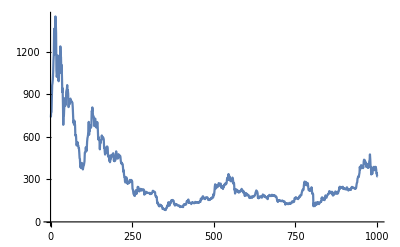

GeometricBrownianMotionProcess[0.000548921,0.0524487,322.452]

```mathematica
Import["https://api.coingecko.com/api/v3/coins/ethereum/market_chart?vs_currency=usd&days=1000","json"];
First[%][[2]];
ethPrices=Transpose[%][[2]];
initPrice=Last[ethPrices];
ListLinePlot[ethPrices,PlotRange->All]
FindProcessParameters[ethPrices,GeometricBrownianMotionProcess[μ,σ,s0]];
gbmp=GeometricBrownianMotionProcess[μ,σ,initPrice]/.%
```

## Monte Carlo: finalPriceMC

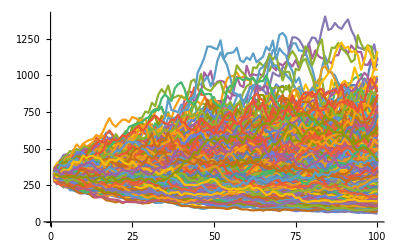

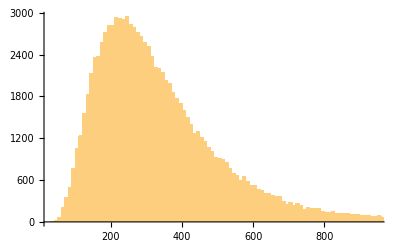

```mathematica
daysMC=100;
trialsMC=100000;

(* Small 100 trial visualization *)

ListLinePlot[RandomFunction[gbmp,{1,daysMC,1},1000],PlotRange->All]
Export[NotebookDirectory[]<>"mc.pdf",%,ImageSize->Small];



(* Histrogram *)

runsMC=RandomFunction[gbmp,{1,daysMC,1},trialsMC];
finalPriceMC=Sort[runsMC["SliceData",daysMC]];
Histogram[%,{10},Axes->{True,False}]
Export[NotebookDirectory[]<>"histro.pdf",%,ImageSize->Small];
```

## RB Coin: Statistics

```mathematica
targetUSD=1;
initialMargin=0.5;

collateralETH =((1+initialMargin)*targetUSD)/initPrice;
collateralUSD=collateralETH*initPrice;
initPriceBlackETH=(collateralETH-targetUSD/initPrice);
initPriceRedETH=initPriceBlackETH/initialMargin;

(* Print Statements *)
Print["Stability target is $",targetUSD, " USD."];
Print["That is ", targetUSD/initPrice, " ETH at the current exchange rate of ",initPrice," USD/ETH."];
Print["Over-collaterialzing by ",initialMargin,  ", the contract holds ",collateralETH ," ETH (worth $",collateralUSD," USD)."];
Print["The break-even exchange rate is ",targetUSD/collateralETH," ETH/USD"]
```

Stability target is $1 USD.

That is 0.00310124 ETH at the current exchange rate of 322.452 USD/ETH.

Over-collaterialzing by 0.5, the contract holds 0.00465185 ETH (worth $1.5 USD).

The break-even exchange rate is 214.968 ETH/USD

## RB Coin: Charts

```mathematica
EvaluateRB [targetUSD_,initialMargin_,curPrice_,finalPriceMC_]:=
Module[{collateralETH,bvalue,evalRB},

collateralETH=((1+initialMargin)*targetUSD)/curPrice;

bvalue[exrate_]:=collateralETH*exrate-targetUSD;

evalRB[exrate_]:=If[bvalue[exrate]<0,
{collateralETH*exrate,0},
{targetUSD,bvalue[exrate]}];

Transpose[evalRB/@finalPriceMC]
]

{finalPriceRed,finalPriceBlack}=EvaluateRB[1,0.5,initPrice,finalPriceMC];

ddd1={finalPriceMC,finalPriceRed}//Transpose;
ddd2={finalPriceMC,finalPriceBlack}//Transpose;
ddd3={finalPriceMC,initPriceRedETH*finalPriceMC}//Transpose;
ddd4={finalPriceMC,initPriceBlackETH*finalPriceMC}//Transpose;
ddd5={finalPriceMC,(initPriceBlackETH+initPriceRedETH)*finalPriceMC}//Transpose;


legend={"Black Coin","Red Coin","ETH ($0.50)"};
ListLinePlot[{ddd1,ddd2,ddd4},Epilog->{Dashed,l1,l2},PlotLegends->legend, PlotStyle->{Black, Red, Purple}]
Export[NotebookDirectory[]<>"price1.pdf",%,ImageSize->Small];

lll[price_]:=Line[{{price,0},{price,Max[finalPriceBlack]}}];
l1=lll[initPrice];
l2=lll[targetUSD/collateralETH];
legend={"Red Coin","ETH ($1.50)","Portfolio"};
ListLinePlot[{ddd2,ddd5,ddd2+0.93},Epilog->{Dashed,l1,l2},PlotLegends->legend,PlotStyle->{Red, Orange, Green}]
Export[NotebookDirectory[]<>"price2.pdf",%,ImageSize->Small];
```

-Graphics-

-Graphics-

## RB Coin: Values

```mathematica
daysMC=100;
trialsMC=100000;
gbmp;
runsMC=RandomFunction[gbmp,{1,daysMC,1},trialsMC];
finalPriceMC=Sort[runsMC["SliceData",daysMC]];

{finalPriceRed,finalPriceBlack}=EvaluateRB[1,0.5,initPrice,finalPriceMC];

Mean[finalPriceRed]
Mean[finalPriceBlack]
```

0.931913

0.652818